## MatLaB Import

### Init

```mathematica
Clear[pathBase,pathSet,pathSubSet,pathSubSubSet,paths,nameSet,nameSubset,nameSubSubset]
pathBase=$HomeDirectory<>"/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/";
pathSet={"GeneralSkin/","IndividualSkin/FSkin/","IndividualSkin/JSkin/","IndividualSkin/NSkin/"};
pathSubSet={{""},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"},{"comb/","Hands/","Index/","Little/","Middle/","Ring/","Thumb/"}};
pathSubSubSet = {{{""}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}},{{""},{"Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"},{"Tip/Orig/","Pad/Orig/"}}};
paths=Table[Table[Table[pathBase<>pathSet[[i]]<>pathSubSet[[i,j]]<>pathSubSubSet[[i,j,k]]<>"mathematica/",{k,1,Length[pathSubSubSet[[i,j]]]}],{j,1,Length[pathSubSet[[i]]]}],{i,1,4}];
nameSet={"RGB_GeneralSkin","RGB_FSkin","RGB_JSkin","RGB_NSkin"};
nameSubset = {{""},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"},{"Comb","Hands","Index","Little","Middle","Ring","Thumb"}};
nameSubSubset = {{{""}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}},{{""},{"Orig"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"},{"Tip","Pad"}}};
```

```mathematica
setupFileSystem[set_,subSet_,subSubSet_]:=Module[{},
(* Set the path : path *)
(* and filenames : *)
(* filenames2D matLabNames2D names2D *)
(* filenames3D matLabNames3D names3D *)
path=paths[[set,subSet,subSubSet]];
Print["Set : ",nameSet[[set]],"     Subset : ",nameSubset[[set,subSet]],"     Subsubset : ",nameSubSubset[[set,subSet,subSubSet]]];
Print["path :",path];
AppendTo[$Path, path];
filenames2D=Sort[StringReplace[FileNames["*CaCb*.mat",path],Evaluate[path]-> ""],StringLength[#1]<StringLength[#2]&];
filenames3D=Sort[Complement[StringReplace[FileNames[__~~".mat",path],Evaluate[path]-> ""],filenames2D],StringLength[#1]<StringLength[#2]&];
Print[TableForm[Transpose[{filenames3D,filenames2D}],TableHeadings->{None,{"3D","2D"}}]];
matLabNames2D=StringReplace[filenames2D,".mat"->""];
matLabNames3D=StringReplace[filenames3D,".mat"->""];
names2D=StringReplace[matLabNames2D,"_"->""];
names3D=StringReplace[matLabNames3D,"_"->""];
Print[TableForm[Transpose[{matLabNames3D,names3D,matLabNames2D,names2D}],TableHeadings->{None,{"3D MatLab","3D Mathematica","2D MatLab","2D Mathematica"}}]];
]
```

#### Import Bins

```mathematica
fields={"name","axisNames","dims","nBins","bin","vals","bins","fBin","g","gMean","gSigma","gTheta","gAmp","aMin","aMax","aScale","count","a","subs","loc"};
```

```mathematica
Clear[ImportMatlabData];
ImportMatlabData[name_,matLabName_,path_]:=Block[{indx},
Clear[Evaluate[Symbol[name]]];
Evaluate[Symbol[name]["name"]]=FromCharacterCode[(Import[(matLabName<>".mat"),{"Data","name"},Path->path])];Evaluate[Symbol[name]["axisNames"]]=Map[("\""<>FromCharacterCode[#]<>"\"")&,(Import[(matLabName<>".mat"),{"Data","axisNames"},Path->path])];Evaluate[Symbol[name]["dims"]]=(Import[(matLabName<>".mat"),{"Data","dims"},Path->path])[[1,1]];Evaluate[Symbol[name]["nBins"]]=(Import[(matLabName<>".mat"),{"Data","nBins"},Path->path])[[1]];
indx=Table[i,{i,Symbol[name]["dims"],1,-1}]; indx[[-2]]=1; indx[[-1]]=2;Evaluate[Symbol[name]["bin"]]=Transpose[Import[(matLabName<>".mat"),{"Data","bin"},Path->path],indx];Evaluate[Symbol[name]["vals"]]=Import[(matLabName<>".mat"),{"Data","vals"},Path->path];Evaluate[Symbol[name]["bins"]]=Import[(matLabName<>".mat"),{"Data","bins"},Path->path];Evaluate[Symbol[name]["fBin"]]=Transpose[Import[(matLabName<>".mat"),{"Data","fBin"},Path->path],indx];Evaluate[Symbol[name]["g"]]=Import[(matLabName<>".mat"),{"Data","g"},Path->path];Evaluate[Symbol[name]["gMean"]]=(Import[(matLabName<>".mat"),{"Data","gMean"},Path->path])[[1]];Evaluate[Symbol[name]["gSigma"]]=(Import[(matLabName<>".mat"),{"Data","gSigma"},Path->path])[[1]];Evaluate[Symbol[name]["gTheta"]]=(Import[(matLabName<>".mat"),{"Data","gTheta"},Path->path])[[1,1]];Evaluate[Symbol[name]["gAmp"]]=(Import[(matLabName<>".mat"),{"Data","gAmp"},Path->path])[[1,1]];Evaluate[Symbol[name]["aMin"]]=(Import[(matLabName<>".mat"),{"Data","aMin"},Path->path])[[1]];Evaluate[Symbol[name]["aMax"]]=(Import[(matLabName<>".mat"),{"Data","aMax"},Path->path])[[1]];Evaluate[Symbol[name]["aScale"]]=Flatten[(Import[(matLabName<>".mat"),{"Data","aScale"},Path->path])];Evaluate[Symbol[name]["count"]]=(Import[(matLabName<>".mat"),{"Data","count"},Path->path])[[1,1]];Evaluate[Symbol[name]["a"]]=Import[(matLabName<>".mat"),{"Data","a"},Path->path];Evaluate[Symbol[name]["subs"]]=Import[(matLabName<>".mat"),{"Data","subs"},Path->path];Evaluate[Symbol[name]["loc"]]=Import[(matLabName<>".mat"),{"Data","loc"},Path->path];
If[Dimensions[Symbol[name]["fBin"]]==Dimensions[Symbol[name]["bin"]],
Print["All's Good"],
Message[ImportMatlabData::fBin,matLabName];
]
]
ImportMatlabData::fBin="The fBin in  `1` has not been normalised."
```

The fBin in  `1` has not been normalised.

#### The Cube objects method for 3D bin plots.

```mathematica
Clear[LCaCbColorFast]
LCaCbColorFast["Hue"][θ_,yIn_,aIn_,bIn_,lIn___]:= Module[{},
Hue[Quiet[Mod[(ArcTan[(aIn-0.5),(bIn-0.5)]-θ-4 Pi/3),2 Pi]/(2 Pi)/.Indeterminate->0,{ArcTan::indet}],
Sqrt[2]*Sqrt[(aIn-0.5)^2+(bIn-0.5)^2],
yIn,lIn]
]
LCaCbColorFast["RGB"][θ_,yIn_,aIn_,bIn_,lIn___]:= Module[{},
ColorConvert[Hue[Quiet[Mod[(ArcTan[(aIn-0.5),(bIn-0.5)]-θ-4 Pi/3),2 Pi]/(2 Pi)/.Indeterminate->0,{ArcTan::indet}],
Sqrt[2]*Sqrt[(aIn-0.5)^2+(bIn-0.5)^2],
yIn,lIn],"RGB"]
]
LCaCbColorFast[colorSpace_][θ_,yIn_,aIn_,bIn_,lIn___]:= Module[{},
ColorConvert[Hue[Quiet[Mod[(ArcTan[(aIn-0.5),(bIn-0.5)]-θ-4 Pi/3),2 Pi]/(2 Pi)/.Indeterminate->0,{ArcTan::indet}],
Sqrt[2]*Sqrt[(aIn-0.5)^2+(bIn-0.5)^2],
yIn,lIn],colorSpace]
]
Clear[SetUpLCaCbColor]
SetUpLCaCbColor[name_:"LCaCbColorFast",θ_,colorSpace_:"Hue"] :=Module[{fun},
fun=Function[{yy,aa,bb,αα},Evaluate[LCaCbColorFast[colorSpace][0,yy,aa,bb,αα]]];
LCaCbColor[List[elem__]]:=LCaCbColor[elem];
ToExpression[name<>"[List[elem__]] := "<>name<>"[elem]"];
ToExpression[name<>"[y_,a_,b_,α_] := Evaluate["<>ToString[fun,InputForm]<>"[y,a,b,α]]"];
ToExpression[name<>"[y_,a_,b_] := Evaluate[("<>ToString[fun,InputForm]<>"[y,a,b,Null])/.Null→Sequence[]]"];
]
```

Test Color setup; the two images should look the same.

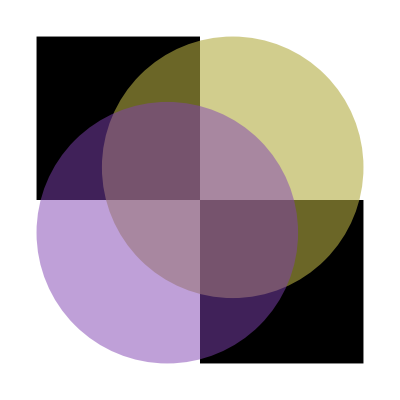
-Graphics--Graphics-

```mathematica
SetUpLCaCbColor["LCaCb",0,"Hue"];Row[{Graphics[{Black,Rectangle[{-1,0.25},{0.25,1.5}],Rectangle[{0.25,-1},{1.5,0.25}],Opacity[0.6],LCaCb[0.7,0.7,0.1],Disk[{0.5,0.5},1],Opacity[0.5],LCaCb[0.7,0.1,0.7],Disk[]}],
Graphics[{Black,Rectangle[{-1,0.25},{0.25,1.5}],Rectangle[{0.25,-1},{1.5,0.25}],LCaCb[0.7,0.7,0.1,0.6],Disk[{0.5,0.5}],LCaCb[0.7,0.1,0.7,0.5],Disk[]}]}]
```

```mathematica
BinPlot3D[bin_,"RGB",tolZero:_:N[1/256],step_:1]:=Module[{r,g,b,rMax,gMax,bMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,fBin},
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.03;(* Opacity min*)
{rMax,gMax,bMax}=Dimensions[bin["fBin"]];
Flatten[{EdgeForm[],Table[
vals= Flatten[(bin["fBin"])[[r;;r+step-1,g;;g+step-1,b;;b+step-1]]];
val=Total[vals]/Length[vals];
If[val>tolZero,
{RGBColor[{r/rMax,g/gMax,b/bMax,(1.-minO)  val+minO}],
Cuboid[{r-1,g-1,b-1},{r+step-1,g+step-1,b+step-1}]
}]
,{r,1,rMax,step},{g,1,gMax,step},{b,1,bMax,step}]}]/.Null-> Sequence[]
]
BinPlot3D[bin_,"LCaCb",tolZero:_:N[1/256],step_:1]:=Module[{l,Ca,Cb,lMax,CaMax,CbMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,fBin},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.03;(* Opacity min*)
{lMax,CaMax,CbMax}=Dimensions[bin["fBin"]];
Flatten[{EdgeForm[],Table[
vals= Flatten[(bin["fBin"])[[l;;l+step-1,Ca;;Ca+step-1,Cb;;Cb+step-1]]];
val=Total[vals]/Length[vals];
If[val>tolZero,
{LCaCbColor[{l/(lMax) (maxL-minL)+minL,Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO}],
Cuboid[{l-1,Ca-1,Cb-1},{l+step-1,Ca+step-1,Cb+step-1}]
}]
,{l,1,lMax,step},{Ca,1,CaMax,step},{Cb,1,CbMax,step}]}]/.Null-> Sequence[]
]
```

```mathematica
HistoPlot3D[bin_,"LCaCb",tolZero:_:N[1/256],drIn_:{}]:=Module[{l,Ca,Cb,lMax,CaMax,CbMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,dr},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.3;(* Opacity min*)
{CaMax,CbMax}=Dimensions[bin["fBin"]];
If[Length[drIn]==0,dr={{1,CaMax},{1,CbMax}},dr=drIn];
Flatten[{EdgeForm[],
Table[val=bin["fBin"][[Ca,Cb]];
If[val>0.001,{EdgeForm[],LCaCbColor[0.7,Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO],Cuboid[{Ca-0.5,Cb-0.5,0},{Ca+0.5,Cb+0.5, bin["fBin"][[Ca,Cb]]}]}],{Cb,dr[[2,1]],dr[[2,2]]},{Ca,dr[[1,1]],dr[[1,2]]}]/.Null->Sequence[]
}]
]
```

```mathematica
Clear[BinPlot2D]
BinPlot2D[bin_,"LCaCb",tolZero:_:N[1/256],step_:1]:=Module[{l,Ca,Cb,CaMax,CbMax,minL,maxL,minO,val,vals,LCaCb,LCaCbA,rgb,fBin},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.03;(* Opacity min*)
{CaMax,CbMax}=Dimensions[bin["fBin"]];
l=0.5;
Flatten[{EdgeForm[],Table[
vals= Flatten[(bin["fBin"])[[Ca;;Ca+step-1,Cb;;Cb+step-1]]];
val=Total[vals]/Length[vals];
If[val>tolZero,
{LCaCbColor[{l,Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO}],
Rectangle[{Ca-1,Cb-1},{Ca+step-1,Cb+step-1}]
}]
,{Ca,1,CaMax,step},{Cb,1,CbMax,step}]}]/.Null-> Sequence[]
]
```

```mathematica
Clear[genAnimation]
genAnimation[bin_,{θs_,θe_},{ϕs_,ϕe_},frames_]:=Module[{i,θ,ϕ=Pi/3,stepθ,stepϕ},
stepθ=(θe-θs)/frames;
stepϕ=(ϕe-ϕs)/frames;
Table[
θ=θs+i stepθ;
ϕ=ϕs+i stepϕ;
Rasterize[Graphics3D[bin["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->bin["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> bin["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> bin["PlotLabel"]]],{i,0,frames,1}]
];
```

```mathematica
boundBox[bin_]:={EdgeForm[{Black,Thick}],FaceForm[],Cuboid[{(bin["aMin"]),(bin["aMax"])}]};
skinnedBox[bin_,skinDepth_]:={EdgeForm[{Black,Thick}],FaceForm[],Cuboid[{(bin["aMin"])+skinDepth, (bin["aMax"])-skinDepth}]};
```

```mathematica
topAndTailBox[bin_,depth_]:={EdgeForm[{Black,Thick}],FaceForm[{White,Opacity[0.4]}],Cuboid[{(bin["aMin"]),{(bin["aMin"])[[1]]+depth,(bin["aMax"])[[2]],(bin["aMax"])[[3]]}}],Cuboid[{{(bin["aMax"])[[1]]-depth,(bin["aMin"])[[2]],(bin["aMin"])[[3]]},(bin["aMax"])}]};
```

```mathematica
projectedView[bin_,extra_:{},n_,opts:OptionsPattern[Graphics3D]]:=Module[{viewPoint,axesLabel,axesEdge},
axesEdge={{-1,-1},{-1,-1},{-1,-1}}; axesEdge[[n]]=None;
axesLabel=bin["axisNames"]; axesLabel[[n]]="";
viewPoint={0,0,0}; viewPoint[[n]]=Infinity;
Rasterize[Graphics3D[{bin["PlotData"],extra},Method->{"CuboidPoints"->4},Axes->True,AxesEdge->axesEdge,AxesLabel->axesLabel,ViewPoint->viewPoint,ImageSize->400,Lighting->"Neutral",opts]]]
```

```mathematica
GaussianFitFun[x_,y_,μ_,σ_,θ_]:=Module[{xrot,yrot,μrot},
xrot=x Cos[θ]-y Sin[θ];
yrot=x Sin[θ]+y Cos[θ];
μrot={μ[[1]]*Cos[θ]-μ[[2]] Sin[θ],μ[[1]] Sin[θ]+μ[[2]]*Cos[θ]};
Exp[-((xrot-μrot[[1]])^2/(2*σ[[1]]^2)+(yrot-μrot[[2]])^2/(2*σ[[2]]^2))]
]
```

```mathematica
Clear[GaussianFit]
GaussianFit[bin_,order_:{1,2}]:=Module[{xx,yy,μ,σ,θ},
μ={bin["gMean"  ][[order[[1]]]],bin["gMean"   ][[order[[2]]]]};
σ={bin["gSigma"][[order[[1]]]],bin["gSigma"][[order[[2]]]]};
If[order=={1,2},θ=Pi-bin["gTheta"],θ=Pi/2-bin["gTheta"]];
Function[{xx,yy},Evaluate[GaussianFitFun[xx,yy,μ,σ,θ]]]
];
```

```mathematica
Clear[MajorMinorAxesPoints];
MajorMinorAxesPoints[μ_,σ_,θ_,sig_]:={
{{μ[[1]]-sig σ[[1]] Cos[θ],μ[[2]] -sig σ[[1]]Sin[θ] },{μ[[1]]+sig σ[[1]]Cos[θ] ,μ[[2]] +sig σ[[1]] Sin[θ] }},
{{μ[[1]]-sig σ[[2]] Cos[θ-Pi/2],μ[[2]] -sig σ[[2]]Sin[θ-Pi/2] },{μ[[1]]+sig σ[[2]]Cos[θ-Pi/2] ,μ[[2]] +sig σ[[2]] Sin[θ-Pi/2] }}};
```

```mathematica
Clear[dataRange]
If[$VersionNumber>9,
dataRange[bin_,"All"]:=Module[{axisTotalA,axisTotalB},
axisTotalA=Total[bin["fBin"],{1}];
axisTotalB=Total[bin["fBin"],{2}];
{Flatten[{FirstPosition[axisTotalB,n_ /; n>0],
Length[axisTotalB]-FirstPosition[Reverse[axisTotalB],n_ /; n>0]}],Flatten[{FirstPosition[axisTotalA,n_ /; n>0],
Length[axisTotalA]-FirstPosition[Reverse[axisTotalA],n_ /; n>0]}]}
],
dataRange[bin_,"All"]:=Module[{axisTotalA,axisTotalB},
axisTotalA=Total[bin["fBin"],{1}];
axisTotalB=Total[bin["fBin"],{2}];
{Flatten[{First[Position[axisTotalB,n_ /; n>0]],
Length[axisTotalB]-First[Position[Reverse[axisTotalB],n_ /; n>0]]}],Flatten[{First[Position[axisTotalA,n_ /; n>0]],
Length[axisTotalA]-First[Position[Reverse[axisTotalA],n_ /; n>0]]}]}
]
]
dataRange[bin_,sig_Integer]:=Module[{μ,σ,θ,mmAxes},
μ={bin["gMean"  ][[1]],bin["gMean"   ][[2]]};
σ={bin["gSigma"][[1]],bin["gSigma"][[2]]};
θ=bin["gTheta"];
mmAxes=MajorMinorAxesPoints[μ,σ,θ,sig];
{{Min[Flatten[mmAxes[[All,All,1]]]],
Max[Flatten[mmAxes[[All,All,1]]]]},{
Min[Flatten[mmAxes[[All,All,2]]]],
Max[Flatten[mmAxes[[All,All,2]]]]}}
]
```

```mathematica
Clear[elipsePlt];
elipsePlt[bin_,sig_:5,order_:{1,2}]:=Module[{μ,σ,θ,mmAxes},
μ={bin["gMean"  ][[order[[1]]]],bin["gMean"   ][[order[[2]]]]};
σ={bin["gSigma"][[order[[1]]]],bin["gSigma"][[order[[2]]]]};
If[order=={1,2},θ=bin["gTheta"],θ=Pi-bin["gTheta"]]; 
{EdgeForm[{Black}],FaceForm[],Table[Rotate[Ellipsoid[Reverse[μ],i σ],Pi/2-θ],{i,1,sig}]}
]
```

```mathematica
fitXPlt[bin_,sig_:5,order_:{1,2}]:=Module[{μ,σ,θ,x1,x2,f1,f2},
μ={bin["gMean"  ][[order[[1]]]],bin["gMean"   ][[order[[2]]]]};
σ={bin["gSigma"][[order[[1]]]],bin["gSigma"][[order[[2]]]]};
If[order=={1,2},θ=bin["gTheta"],θ=Pi-bin["gTheta"]];
Show[Table[
x1=μ[[2]]-i σ[[1]];x2=μ[[2]]+i σ[[1]];
f1=GaussianFitFun[x1,μ[[1]],Reverse[μ],σ,0];
f2=GaussianFitFun[x2,μ[[1]],Reverse[μ],σ,0];
{ListPlot[{{x1,f1},{x2,f2}},Frame->True,Axes->False,PlotStyle->Red],Graphics[{Text[i"σ_1",{x1,f1},{1,-1}],Text[i"σ_1",{x2,f2},{-1,-1}]}]},{i,1,sig}],Plot[GaussianFitFun[x,μ[[1]],Reverse[μ],σ,0],{x,μ[[2]]-5 σ[[1]],μ[[2]]+5 σ[[1]]},AxesLabel->{"Cb'","Frequency"},PlotStyle->Red],PlotRange->{{μ[[2]]-5.2 σ[[1]],μ[[2]]+5.2 σ[[1]]},{0,1}},FrameLabel->{{"Frequency",None},{"Cb'","The σ_1 Gaussian"}}]
];

fitYPlt[bin_,sig_:5,order_:{1,2}]:=Module[{μ,σ,θ,y1,y2,f1,f2},
μ={bin["gMean"  ][[order[[1]]]],bin["gMean"   ][[order[[2]]]]};
σ={bin["gSigma"][[order[[1]]]],bin["gSigma"][[order[[2]]]]};
If[order=={1,2},θ=bin["gTheta"],θ=Pi-bin["gTheta"]];
Show[Table[
y1=μ[[1]]-i σ[[2]];y2=μ[[1]]+i σ[[2]];
f1=GaussianFitFun[μ[[2]],y1,Reverse[μ],σ,0];
f2=GaussianFitFun[μ[[2]],y2,Reverse[μ],σ,0];
{ListPlot[{{y1,f1},{y2,f2}},Frame->True,Axes->False,PlotStyle->Green],Graphics[{Text[i"σ_2",{y1,f1},{1,-1}],Text[i"σ_2",{y2,f2},{-1,-1}]}]},{i,1,sig}],Plot[GaussianFitFun[μ[[2]],y,Reverse[μ],σ,0],{y,μ[[1]]-5 σ[[2]],μ[[1]]+5 σ[[2]]},AxesLabel->{"Ca'","Frequency"},PlotStyle->Green],PlotRange->{{μ[[1]]-5.2 σ[[2]],μ[[1]]+5.2 σ[[2]]},{0,1}},FrameLabel->{{"Frequency",None},{"Ca'","The σ_2 Gaussian"}}]
];
```

```mathematica
Clear[fit2DLinesPlt]
fit2DLinesPlt[bin_,sig_:5,order_:{1,2}]:=Module[{sr=0.25,μr=1, opcty=0.6},
μ={bin["gMean"  ][[order[[1]]]],bin["gMean"   ][[order[[2]]]]};
σ={bin["gSigma"][[order[[1]]]],bin["gSigma"][[order[[2]]]]};
If[order=={1,2},θ=bin["gTheta"],θ=Pi-bin["gTheta"]];
Do[mmAxes[i]=MajorMinorAxesPoints[μ,σ,θ,i],{i,1,sig}];
axesPltPnts={Opacity[opcty],Blue,Disk[Reverse[μ],sr],
Red,Table[{Disk[mmAxes[i][[1,1]],sr],Disk[mmAxes[i][[1,2]],sr]},{i,1,sig}],
Green, Table[{Disk[mmAxes[i][[2,1]],sr],Disk[mmAxes[i][[2,2]],sr]},{i,1,sig}],
Green,Disk[Reverse[μ],μr,{Pi/2-θ,Pi/2}]};
axesPltLines={Opacity[1],Red,Line[mmAxes[5][[1]]],
Green, Line[mmAxes[5][[2]]]};
axesPltTxt={Opacity[1],Black,
Table[{Text[Style[Subscript[i "σ",Style["1",Small]],Bold],mmAxes[i][[1,1]],{1,1}],Text[Style[Subscript[i "σ",Style["1",Small]],Bold],mmAxes[i][[1,2]],{-1,-1}]},{i,1,5}],Table[{Text[Style[Subscript[i "σ",Style["2",Small]],Bold,Medium],mmAxes[i][[2,1]],{1,0}],Text[Style[Subscript[i "σ",Style["2",Small]],Bold],mmAxes[i][[2,2]],{-1,0}]},{i,1,5}],
Text[Style["μ",Bold],Reverse[μ]+{(-2sr /3) Cos[(Pi/2-θ)],(-2sr /3)  Sin[(Pi/2-θ)]}],
Text[Style["θ",Bold,Large],Reverse[μ]+{(2μr/3) Cos[Pi/2-θ/2],(2μr /3)  Sin[Pi/2-θ/2]}]};
{axesPltPnts,axesPltLines,axesPltTxt}
]
```

```mathematica
fit2DAnglePlt[bin_,order_:{1,2}]:=Module[{r=4, opcty=0.6},
μ={bin["gMean"  ][[order[[1]]]],bin["gMean"   ][[order[[2]]]]};
σ={bin["gSigma"][[order[[1]]]],bin["gSigma"][[order[[2]]]]};
If[order=={1,2},θ=bin["gTheta"],θ=Pi-bin["gTheta"]];
{Graphics[{Opacity[opcty],Green,
Disk[Reverse[μ],r,{Pi/2-θ,Pi/2}],Opacity[1],Black,Text[Style["θ",Bold,Large],Reverse[μ]+{(2r /3) Cos[Pi/2-θ/2],(2r /3)  Sin[Pi/2-θ/2]}]}]
,Graphics[{Opacity[opcty],Red,Disk[Reverse[μ],r,{0,Pi/2-θ}],Opacity[1],Black,Text[Style[π/2-"θ",Bold],Reverse[μ]+{(2r /3) Cos[(Pi/2-θ)/2],(2r /3)  Sin[(Pi/2-θ)/2]}]}]}
];
```

#### Junk

```mathematica
Clear[AddRGBValuesToBin]
AddRGBValuesToBin[bin_,"RGB",tolZero:_:N[1/256]]:=Module[{r,g,b,rMax,gMax,bMax,minL,maxL,minO,val,LCaCb,LCaCbA,rgb,fBin},
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.3;(* Opacity min*)
{rMax,gMax,bMax}=Dimensions[bin["fBin"]];
Table[
val=(bin["fBin"])[[r,g,b]];
{r/rMax,g/gMax,b/bMax,(1.-minO)  val+minO}
,{r,1,rMax},{g,1,gMax},{b,1,bMax}]
]
AddRGBValuesToBin[bin_,"LCaCb",tolZero:_:N[1/256]]:=Module[{l,Ca,Cb,lMax,CaMax,CbMax,minL,maxL,minO,val,LCaCb,LCaCbA,rgb,fBin},
SetUpLCaCbColor["LCaCbColor",0];
minL=0.2;(*Black is ok but hard to print*)
maxL=0.8;(* we cant see white on white *)
minO=0.3;(* Opacity min*)
{lMax,CaMax,CbMax}=Dimensions[bin["fBin"]];
Table[val=(bin["fBin"])[[l,Ca,Cb]];
col=ColorConvert[LCaCbColor[{l/(lMax) (maxL-minL)+minL,Ca/CaMax,Cb/CbMax,(1.-minO)  val+minO}],"RGB"];
List@@col
,{l,1,lMax},{Ca,1,CaMax},{Cb,1,CbMax}]
]
```

Generate Raster data

```mathematica
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[Symbol[name<>"3DValues"]]=AddRGBValuesToBin[Symbol[name],"RGB"],
Evaluate[Symbol[name<>"3DValues"]]=AddRGBValuesToBin[Symbol[name],"LCaCb"]
];
Dimensions[Symbol[name<>"3DValues"]]
```

StringFreeQ::strse: String or list of strings expected at position 1 in StringFreeQ[name, _ ~~ "Rot" ~~ ___].

StringJoin::string: String expected at position 1 in name <> "3DValues".

Symbol::string: String expected at position 1 in Symbol[name <> "3DValues"].

{1}

### Set name and path to the matlab stats

```mathematica
TableForm[Table[{i,nameSet[[i]],nameSubset[[i]]},{i,1,Length[nameSet]}],TableHeadings->{None,{"Set","","Subsets"}}]
```

Set |  | Subsets
1 | RGB_GeneralSkin | 
2 | RGB_FSkin | Hands
Index
Little
Middle
Ring
Thumb
3 | RGB_JSkin | Hands
Index
Little
Middle
Ring
Thumb
4 | RGB_NSkin | Hands
Index
Little
Middle
Ring
Thumb

```mathematica
TabView[Table[nameSet[[i]]-> Column[{nameSet[[i]],
If[Length[nameSubset[[i]]]>1,
  TabView[ Table[nameSubset[[i,j]]-> Column[{nameSubset[[i,j]],
  If[Length[nameSubSubset[[i,j]]]>1,
     TabView[ Table[nameSubSubset[[i,j,k]]-> Column[{nameSubSubset[[i,j,k]],
     Button["Set",set=ii;subSet=jj;subSubSet=kk; setupFileSystem[ii,jj,kk]]/.{ii->i,jj-> j,kk->k}
     }],{k,1,Length[nameSubSubset[[i,j]]]}]],
     Button["Set",set=ii;subSet=jj;subSubSet=1; setupFileSystem[ii,jj,1]]/.{ii->i,jj-> j}
  ]
  }],{j,1,Length[nameSubset[[i]]]}] ],
   If[Length[nameSubSubset[[i,1]]]>1,
     TabView[ Table[nameSubSubset[[i,1,k]]-> Column[{nameSubSubset[[i,1,k]],
     Button["Set",set=ii;subSet=1;subSubSet=kk; setupFileSystem[ii,1,kk]]/.{ii->i,kk->k}
     }],{k,1,Length[nameSubSubset[[i,1]]]}]],
     Button["Set",set=ii;subSet=1;subSubSet=1; setupFileSystem[ii,1,1]]/.{ii->i}
  ]
]
}],{i,1,Length[nameSet]}]]
```

1234

Set : RGB_FSkin     Subset : Comb     Subsubset :

path :/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/comb/mathematica/

Transpose[{{RGB_FSkin_Bin.mat},{}}]

Transpose[{{RGB_FSkin_Bin},{RGBFSkinBin},{},{}}]

Import and Generate Data

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

RGB_GeneralSkin_Bin

RGBGeneralSkinBin

### Import and Generate Data

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : RGB_GeneralSkin_Bin

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_GeneralSkin_Bin |  | 
axisNames | R | G | B
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | Transpose[Partition[{},0.]] |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 255. | 255. | 255.
aScale | 255. | 255. | 255.
count | 3.50054×10^6 |  | 
a | Transpose[Partition[{},0.]] |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
256
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/RGB_GeneralSkin_Bin_Animation/RGB_GeneralSkin_Bin.gif

## 2. Skin the Bins

### Import and Generate Data

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : RGB_GeneralSkin_Bin_Skinned

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_GeneralSkin_Bin_Skinned |  | 
axisNames | R | G | B
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | Transpose[Partition[{},0.]] |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 255. | 255. | 255.
aScale | 255. | 255. | 255.
count | 3.50001×10^6 |  | 
a | Transpose[Partition[{},0.]] |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
256
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/RGB_GeneralSkin_Bin_Skinned_Animation/RGB_GeneralSkin_Bin_Skinned.gif

## 3. Rotate the Bins

### Import and Generate Data

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : RGB_GeneralSkin_Bin_Skinned_Rot

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_GeneralSkin_Bin_Skinned |  | 
axisNames | L | Ca | Cb
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | Transpose[Partition[{},0.]] |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 256. | 256. | 256.
aScale | 256. | 256. | 256.
count | 3.50001×10^6 |  | 
a | Transpose[Partition[{},0.]] |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
257
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
StringFreeQ[name,_~~"Rot"~~___]
```

False

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/RGB_GeneralSkin_Bin_Skinned_Rot_Animation/" already exists.

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/RGB_GeneralSkin_Bin_Skinned_Rot_Animation/RGB_GeneralSkin_Bin_Skinned_Rot.gif

## 4. Top and Tail the Bins

### Import and Generate Data

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : RGB_GeneralSkin_Bin_Skinned_Rot_TopTail

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Correct Axes names

```mathematica
If[stage<3,
Symbol[name]["axisNames"]={"R","G","B"},
Symbol[name]["axisNames"]={"L","Ca","Cb"}
];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail |  | 
axisNames | L | Ca | Cb
dims | 3. |  | 
nBins | 256. | 256. | 256.
g | Transpose[Partition[{},0.]] |  | 
gMean | 0. | 0. | 
gSigma | 0. | 0. | 
gTheta | 0. |  | 
gAmp | 1. |  | 
aMin | 0. | 0. | 0.
aMax | 256. | 256. | 256.
aScale | 256. | 256. | 256.
count | 3.36933×10^6 |  | 
a | Transpose[Partition[{},0.]] |  | Dimensions[bin]  | 256
256
256
Dimensions[vals]  | 3
256
Dimensions[bins]  | 3
257
Dimensions[fBin]  | 256
256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=4; 
emptyTol = N[1/256];
If[StringFreeQ[name,_~~"Rot"~~___],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"RGB",emptyTol,pltCubeScale],
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot3D[Symbol[name],"LCaCb",emptyTol,pltCubeScale]
];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

#### Generate the Animation

```mathematica
nFrames=24;
Clear[Evaluate[(name<>"Frames")]]
Evaluate[Symbol[name<>"Frames"]]=genAnimation[Symbol[name],{Pi/6,Pi/6},{0,Pi/2},nFrames];
```

Save animation frames

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name<>"Frames"]]
```

Export the animation

```mathematica
CreateDirectory[path<>matLabName<>"_Animation"];
Block[{aFrame=Symbol[name<>"Frames"]},
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,1,nFrames+1}];
Do[
Export[path<>matLabName<>"_Animation"<>"/frame"<>ToString[NumberForm[2 nFrames+2-i,{3,0},NumberPadding->{"0","0"}]]<>".png", aFrame[[i]], "VideoFrames"],{i,nFrames,1,-1}];
Export[path<>matLabName<>"_Animation"<>"/"<>matLabName<>".gif",Flatten[{aFrame,Reverse[aFrame]}]]
]
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_Animation/RGB_GeneralSkin_Bin_Skinned_Rot_TopTail.gif

## 5. Collapse the Bins

### Import and Generate Data

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb

RGBGeneralSkinBinSkinnedRotTopTailCaCb

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca","Cb"};
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_bc | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | Transpose[Partition[{},0.]] | 
gMean | 0. | 0.
gSigma | 0. | 0.
gTheta | 0. | 
gAmp | 1. | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 3.36933×10^6 | 
a | Transpose[Partition[{},0.]] | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/256];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 6. Despeckle the Bins

### Import and Generate Data

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec

RGBGeneralSkinBinSkinnedRotTopTailCaCbDespec

#### Import Data

```mathematica
Print["Loading : "<>matLabName]
ImportMatlabData[name,matLabName,path]
```

Loading : RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Correct Axes names

```mathematica
Symbol[name]["axisNames"]={"Ca","Cb"};
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Save[path<>"Data"<>"/"<>matLabName<>".m",name];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/" already exists.

Check the import

```mathematica
Row[{TableForm[Map[(Symbol[name][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[name][#]]})&,fields[[5;;8]]]]}]
```

name | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_bc | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | Transpose[Partition[{},0.]] | 
gMean | 0. | 0.
gSigma | 0. | 0.
gTheta | 0. | 
gAmp | 1. | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 3.36933×10^6 | 
a | Transpose[Partition[{},0.]] | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[name<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[name],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[name<>"[\"PlotRange\"]"]] = Transpose[{Symbol[name]["aMin"],Symbol[name]["aMax"]}];
Evaluate[ToExpression[name<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[name]["name"],"_"-> " "];
If[Length[ToExpression[name<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]]
If[Length[ToExpression[name<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]]
```

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]]
names=names2D[[stage-4;;]]
```

{RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2,RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1}

{RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1}

### Import and Generate Data

#### Import Data

```mathematica
Do[
Print["Loading : "<>matLabNames[[i]]];
ImportMatlabData[names[[i]],matLabNames[[i]],path],
{i,1,Length[names]}]
```

Loading : RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Loading : RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1

Correct Axes names

```mathematica
Do[Symbol[names[[i]]]["axisNames"]={"Ca","Cb"},
{i,1,Length[names]}];
```

Save Definitions to Data Directory

```mathematica
CreateDirectory[path<>"Data"];
Do[Print["Saving : "<> names[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames[[i]]<>".m"];
Save[path<>"Data"<>"/"<>matLabNames[[i]]<>".m",Evaluate[names[[i]]]],
{i,1,Length[names]}];
```

CreateDirectory::filex: "/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/" already exists.

Saving : RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

Saving : RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/Data/RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.m

```mathematica
Save[path<>"Data"<>"/"<>matLabNames[[1]]<>".m",Evaluate[names[[1]]] ]
```

Check the import

```mathematica
RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob2["name"]
```

RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob2[name]

```mathematica
Do[Print[Row[{TableForm[Map[(Symbol[names[[i]]][#])&,Flatten[{fields[[1;;4]],fields[[9;;18]]}]],TableHeadings-> {Flatten[{fields[[1;;4]],fields[[9;;18]]}],None}],
TableForm[Map[({Row[{"Dimensions[",#,"] "}],Dimensions[Symbol[names[[i]]][#]]})&,fields[[5;;8]]]]}]],
{i,1,Length[names]}]
```

name | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_bc blob2 | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | Transpose[Partition[{},0.]] | 
gMean | 120.468 | 86.3373
gSigma | 0.233664 | 0.224439
gTheta | -0.110655 | 
gAmp | 0.999985 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 6927. | 
a | 121.
87. | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

name | RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_bc blob1 | 
axisNames | Ca | Cb
dims | 2. | 
nBins | 256. | 256.
g | Transpose[Partition[{},0.]] | 
gMean | 123.054 | 106.536
gSigma | 1.18262 | 5.16078
gTheta | -0.128541 | 
gAmp | 0.9 | 
aMin | 0. | 0.
aMax | 256. | 256.
aScale | 256. | 256.
count | 3.19124×10^6 | 
a | 122.971
103.689 | Dimensions[bin]  | 256
256
Dimensions[vals]  | 2
256
Dimensions[bins]  | 2
257
Dimensions[fBin]  | 256
256

#### Generate the Plot Data

```mathematica
Do[
pltCubeScale=1; 
emptyTol = N[1/1024];
Evaluate[ToExpression[names[[i]]<>"[\"PlotData\"]"]]=BinPlot2D[Symbol[names[[i]]],"LCaCb",emptyTol,pltCubeScale];
Evaluate[ToExpression[names[[i]]<>"[\"PlotRange\"]"]] = Transpose[{Symbol[names[[i]]]["aMin"],Symbol[names[[i]]]["aMax"]}];
Evaluate[ToExpression[names[[i]]<>"[\"PlotLabel\"]"]] = StringReplace[Symbol[names[[i]]]["name"],"_"-> " "];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]>80000,Print["Increase pltCubeScale or emptyTol to reduce the number of cubes"]];
If[Length[ToExpression[names[[i]]<>"[\"PlotData\"]"]]<10000,Print["Decrease pltCubeScale or emptyTol to increase the number of cubes"]],
{i,1,Length[names]}]
```

Decrease pltCubeScale or emptyTol to increase the number of cubes

Decrease pltCubeScale or emptyTol to increase the number of cubes

Save Definitions to Data Directory

```mathematica
Save[path<>"Data"<>"/"<>matLabName<>".m",Evaluate[name]]
```

Generate the Plot Notebook

```mathematica
outputNotebook=path<>"plots.nb"
```

/Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/GeneralSkin/mathematica/plots.nb

```mathematica
nb=CreateDocument[];
```

```mathematica
Clear[NotebookDefinitionWrite]
SetAttributes[NotebookDefinitionWrite,HoldAllComplete]
NotebookDefinitionWrite[nb_,var_]:=Module[{cell},
cell=Cell[BoxData[RowBox[{var,"=",ToBoxes[Symbol[var]],";"}]],"Input"];
NotebookWrite[nb,cell ]]
```

```mathematica
NotebookWrite[nb,Cell["Init","Section"]]
NotebookDefinitionWrite[nb,"path"]
NotebookDefinitionWrite[nb,"filenames2D"]
NotebookDefinitionWrite[nb,"matLabNames2D"]
NotebookDefinitionWrite[nb,"names2D"]
NotebookDefinitionWrite[nb,"filenames3D"]
NotebookDefinitionWrite[nb,"matLabNames3D"]
NotebookDefinitionWrite[nb,"names3D"]
```

```mathematica
NotebookSave[nb,outputNotebook]
```

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

RGB_GeneralSkin_Bin

RGBGeneralSkinBin

### Generate the Plot Notebook

```mathematica
stage=1;
NotebookWrite[nb,Cell["1. Fill the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[1]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

## 2. Skin the Bins

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Generate the Plot Notebook

```mathematica
stage=2;
NotebookWrite[nb,Cell["2. Skin the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[2]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

## 3. Rotate the Bins

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Generate the Plot Notebook

```mathematica
stage=3;
NotebookWrite[nb,Cell["3. Rotate the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[3]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}],",",RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{"boundBox","[",names3D[[stage]],"]"}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

## 4. Top and Tail the Bins

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Generate the Plot Notebook

```mathematica
stage=4;
depth=42;
NotebookWrite[nb,Cell["4. Top and Tail the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[4]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

## 5. Collapse the Bins

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb

RGBGeneralSkinBinSkinnedRotTopTailCaCb

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["5. Collapse the Bins","Section"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[1]]<>".m")],"]",";"}]],"Input"] ]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"GraphicsRow","[",RowBox[{"{",RowBox[{RowBox[{"ListDensityPlot","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[1]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"FrameLabel","→",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"InterpolationOrder","→","0"}]}],"]"}],",",RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],"}"}],"]"}]],"Input"]]
```

## 6. Despeckle the Bins

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec

RGBGeneralSkinBinSkinnedRotTopTailCaCbDespec

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["6. Despeckle the Bins","Section"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Input"] ],
{i,1,Length[names2D]}]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","dr",",","windows",",","blobPlt",",","blobsPlt",",","blobsDespecPlt"}],"}"}],",","
",RowBox[{RowBox[{"dr","=",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","\n",RowBox[{"windows","=",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(",RowBox[{"dr","[",RowBox[{"[","i","]"}],"]"}],")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"ToString","[","i","]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{"i",",","1",",",RowBox[{"Length","[","dr","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}]}],";","
","\n",RowBox[{"blobPlt"," ","="," ",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{"windows",",","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotRange\>\"","]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
","\n",RowBox[{"blobsPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"blobsDespecPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}],"<>","\"\< Despeckled\>\""}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}]}],"\n","]"}]],"Code"]
]
```

```mathematica
NotebookWrite[nb,Cell["Surface plots","Subsection"]]
NotebookWrite[nb,Cell[BoxData[
RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{"dr",",","hist",",","histoPlt",",","surfHistPlt"}],"}"}],",","
",RowBox[{RowBox[{"dr","=",RowBox[{"Round","[",RowBox[{"dataRange","[",RowBox[{names2D[[2]],",","\"\<All\>\""}],"]"}],"]"}]}],";","
",RowBox[{"hist","=",RowBox[{"HistoPlot3D","[",RowBox[{names2D[[2]],",","\"\<LCaCb\>\"",",",RowBox[{"N","[",RowBox[{"1","/","1024"}],"]"}],",","dr"}],"]"}]}],";","
",RowBox[{"histoPlt","=",RowBox[{"Graphics3D","[",RowBox[{"hist",",",RowBox[{"Lighting","→","\"\<Neutral\>\""}],",",RowBox[{"Axes","->","True"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"BoxRatios","→",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"Max","[",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],"]"}]}],"]"}],",","1"}],"}"}],"]"}]}]}],"]"}]}],";","
",RowBox[{"surfHistPlt","=",RowBox[{"ListPlot3D","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[2]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"ColorFunction","→",RowBox[{"Function","[",RowBox[{RowBox[{"{",RowBox[{"x",",","y",",","z"}],"}"}],",",RowBox[{"LCaCbColor","[",RowBox[{"{",RowBox[{"0.5",",","x",",","y"}],"}"}],"]"}]}],"]"}]}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"PlotRange","→","dr"}]}],"]"}]}],";","
",RowBox[{"GraphicsRow","[",RowBox[{"{",RowBox[{"histoPlt",",","surfHistPlt"}],"}"}],"]"}]}]}],"
","]"}]
],"Input"]]
```

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]]
names=names2D[[stage-4;;]]
```

{RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2,RGB_GeneralSkin_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1}

{RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2,RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob1}

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["7. Find the Blobs","Section"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Input"] ],
{i,3,Length[names2D]}];
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","blobPlt",",","blobsPlt"}],"}"}],",",RowBox[{RowBox[{"blobPlt","=",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","[",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}]}],";",RowBox[{"{",RowBox[{RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","2",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}],",",RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(","dr",")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[2]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
",RowBox[{"blobsPlt","=",RowBox[{"Table","[","
",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}]}],";","
",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","2",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ","dr"}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}]}],"}"}]}],"}"}]}]}],"]"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}]}],"
","]"}]],"Input"]
]
```

## 8. Fit the Gaussian

```mathematica
blob=0;
name=names2D[[3+blob]]
```

RGBGeneralSkinBinSkinnedRotTopTailCaCbDespecblob2

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["8. Fit the Gaussian","Section"]]
```

```mathematica
Do[
NotebookWrite[nb,Cell["Blob : "<>ToString[blob],"Subsection"]];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"blob","=","0"}],",","redPlt",",","greenPlt",",","denPlt",",","denOpacityPlt",",","axesPlt",",","elpsPlt",",","thetaPlt",",","thetaPi2Plt",",","histoPlt",",","fitPlt",",","combPlt3D",",","aspctRatio",",","combPlt",",","overviewPlt"}],"}"}],",","
",RowBox[{RowBox[{"redPlt","=",RowBox[{"fitXPlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],";","
",RowBox[{"greenPlt","=",RowBox[{"fitYPlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],";","
","
",RowBox[{"denPlt","=",RowBox[{"ListDensityPlot","[",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fBin\>\"","]"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Cb\>\"",",","\"\<Ca\>\""}],"}"}]}],",",RowBox[{"InterpolationOrder","→","0"}]}],"]"}]}],";","
",RowBox[{"denOpacityPlt","=",RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[3+blob]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",","\"\<Overview\>\""}],"}"}]}],"}"}]}]}],"]"}]}],";","
","
",RowBox[{"axesPlt","=",RowBox[{"Graphics","[",RowBox[{"fit2DLinesPlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],"]"}],"]"}]}],";","
","
",RowBox[{"elpsPlt","=",RowBox[{"Graphics","[",RowBox[{"elipsePlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}],"]"}]}],";","
","
",RowBox[{RowBox[{"{",RowBox[{"thetaPlt",",","thetaPi2Plt"}],"}"}],"=",RowBox[{"fit2DAnglePlt","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],";","
","
",RowBox[{"dr","=",RowBox[{"Round","[",RowBox[{"dataRange","[",RowBox[{names2D[[3+blob]],",","\"\<All\>\""}],"]"}],"]"}]}],";","
",RowBox[{"histoPlt","=",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"HistoPlot3D","[",RowBox[{names2D[[3+blob]],",","\"\<LCaCb\>\"",",",RowBox[{"N","[",RowBox[{"1","/","1024"}],"]"}],",","dr"}],"]"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}],",",RowBox[{"Axes","->","True"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"BoxRatios","→",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"Max","[",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],"]"}]}],"]"}],",","1"}],"}"}],"]"}]}]}],"]"}]}],";","
",RowBox[{"fun","=",RowBox[{"GaussianFit","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],"]"}]}],";","
",RowBox[{"fitPlt","=",RowBox[{"Plot3D","[",RowBox[{RowBox[{"fun","[",RowBox[{"x",",","y"}],"]"}],",",RowBox[{"{",RowBox[{"x",",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"y",",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"PlotRange","→",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"}"}]}],",",RowBox[{"PlotPoints","→",RowBox[{"2"," ",RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}]}],")"}]}]}],",",RowBox[{"PlotStyle","→",RowBox[{"LCaCbColor","[",RowBox[{"{",RowBox[{"0.7",",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<gMean\>\"","]"}],"[",RowBox[{"[","1","]"}],"]"}],"/","255"}],",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<gMean\>\"","]"}],"[",RowBox[{"[","2","]"}],"]"}],"/","255"}],",","0.6"}],"}"}],"]"}]}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"MeshFunctions","->",RowBox[{"{",RowBox[{"#3","&"}],"}"}]}]}],"]"}]}],";","
",RowBox[{"combPlt3D","=",RowBox[{"Show","[",RowBox[{RowBox[{"{",RowBox[{"fitPlt",",","histoPlt"}],"}"}],",","
",RowBox[{"PlotRange","→",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"}"}]}],",","
",RowBox[{"BoxRatios","→",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"Max","[",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],"]"}]}],"]"}],",","1"}],"}"}],"]"}]}]}],"]"}]}],";","
","
",RowBox[{"dr","=",RowBox[{"dataRange","[",RowBox[{names2D[[3+blob]],",","5"}],"]"}]}],";","
",RowBox[{"aspctRatio","=",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}]}],")"}]}]}],";","
",RowBox[{"combPlt","=",RowBox[{"Show","[",RowBox[{RowBox[{"{",RowBox[{"denOpacityPlt",",","axesPlt",",","elpsPlt",",","
","thetaPlt"}],"}"}],",",RowBox[{"PlotRange","→","dr"}],",",RowBox[{"AspectRatio","→",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}]}],")"}]}]}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{"\"\<Cb\>\"",",","\"\<Ca\>\""}],"}"}]}]}],"]"}]}],";","
",RowBox[{"overviewPlt","=",RowBox[{"Show","[",RowBox[{"{",RowBox[{"denOpacityPlt",",",RowBox[{"Graphics","[",RowBox[{"{",RowBox[{RowBox[{"FaceForm","[","]"}],",",RowBox[{"EdgeForm","[",RowBox[{"{",RowBox[{"Black",",",RowBox[{"Opacity","[","1","]"}]}],"}"}],"]"}],",",RowBox[{"Rectangle","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}]}],"]"}]}],"}"}],"]"}]}],"}"}],"]"}]}],";","
","
",RowBox[{"TabView","[",RowBox[{"{",RowBox[{RowBox[{"If","[",RowBox[{RowBox[{"aspctRatio","≥","1"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D",",","         ","SpanFromLeft",",","combPlt",",","             ","SpanFromLeft",",","overviewPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D",",","SpanFromLeft",",","combPlt",",","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromLeft",",","overviewPlt",",","redPlt",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}],"]"}],",","
",RowBox[{"If","[",RowBox[{RowBox[{"aspctRatio","≥","1"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt",",","             ","SpanFromLeft",",","overviewPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","redPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt",",","SpanFromLeft",",","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt",",","redPlt",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}],"]"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]
],{blob,0,Length[names2D]-3}]
```

## Save the notebook

```mathematica
NotebookSave[nb,outputNotebook]
```

## That RGB Image check thing.

```mathematica
img=-Graphics-;
```

```mathematica
imgData=Flatten[ImageData[img,"Byte"],1];
```

```mathematica
bins=ConstantArray[0,{256,256,256}];
```

```mathematica
Do[
bins[[ imgData[[i,1]]+1, imgData[[i,2]]+1, imgData[[i,3]]+1 ]]++;
,{i,1,Dimensions[imgData][[1]] }]
```

```mathematica
Dimensions[bins]
```

{256,256,256}

```mathematica
Max[Flatten[bins]]
```

5

```mathematica
Position[bins,n_/;n==5]
```

{{1,256,256}}

```mathematica
pos=Position[ImageData[img,"Byte"],n_/;n=={0,255,255}]
```

{{852,121},{853,120},{859,121},{867,114},{871,120}}

Are they all really {0,255,255}

```mathematica
Table[ImageData[img,"Byte"][[pos[[i,1]],pos[[i,2]]]],{i,1,Length[pos]}]
```

{{0,255,255},{0,255,255},{0,255,255},{0,255,255},{0,255,255}}

```mathematica
Count[bins,n_/;n>1,3]
```

34938

```mathematica
Dimensions[ImageData[img,"Byte"]]
```

{1024,1024,3}

```mathematica
Show[{img,Graphics[{Table[Circle[pos[[i]],10],{i,1,Length[pos]}]}]}]
```

-Graphics-

Plot the bins

## 1. Fill the Bins

```mathematica
stage=1;
matLabName=matLabNames3D[[stage]]
name=names3D[[stage]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"];
```

### Generate the Plot Notebook

```mathematica
stage=1;
NotebookWrite[nb,Cell["1. Fill the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[1]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

### Plot the Bin

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView,skinDepth=9},isoView=Rasterize[Graphics3D[Symbol[name]["PlotData"],Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 2. Skin the Bins

```mathematica
stage=2;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Generate the Plot Notebook

```mathematica
stage=2;
NotebookWrite[nb,Cell["2. Skin the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[2]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView,skinDepth=9},isoView=Rasterize[Graphics3D[Symbol[name]["PlotData"],Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],skinnedBox[Symbol[name],skinDepth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 3. Rotate the Bins

```mathematica
stage=3;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Generate the Plot Notebook

```mathematica
stage=3;
NotebookWrite[nb,Cell["3. Rotate the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[3]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
```

```mathematica
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView"}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}],",",RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",",","0"}],"}"}]}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{"boundBox","[",names3D[[stage]],"]"}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"topAndTailBox","[",RowBox[{names3D[[stage]],",","depth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[names3D[[3]]]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[names3D[[3]]]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[names3D[[3]]]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[names3D[[3]]]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[names3D[[3]]<>"Frames"],AnimationDirection->ForwardBackward]
```

$Aborted[]

#### Show the Projected views

```mathematica
depth=42;
```

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView},isoView=Rasterize[Graphics3D[{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth],Symbol[names3D[[3]]]["PlotData"]},Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewVertical->{1,0,0},ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[names3D[[3]]]["axisNames"],ImageSize->400,Lighting->"Neutral"]];
redView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]]},1];
greenView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth]},2];
blueView=projectedView[Symbol[names3D[[3]]],{boundBox[Symbol[names3D[[3]]]],topAndTailBox[Symbol[names3D[[3]]],depth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 4. Top and Tail the Bins

```mathematica
stage=4;
matLabName=matLabNames3D[[stage]];
name=names3D[[stage]];
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"]
```

### Generate the Plot Notebook

```mathematica
stage=4;
NotebookWrite[nb,Cell["4. Top and Tail the Bins","Section"]]
NotebookWrite[nb,Cell["Load previously generated data","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames3D[[4]]<>".m")],"]",";"}]],"Input"] ]
NotebookWrite[nb,Cell["Plot the Bin","Subsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{RowBox[{"Manipulate","[","
",RowBox[{RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",","
",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewAngle","→",RowBox[{"Pi","/","7"}]}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImagePadding","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"2",",","2"}],"}"}],",",RowBox[{"{",RowBox[{"2",",","2"}],"}"}]}],"}"}]}],",",RowBox[{"ImageSize","→","400"}],",",RowBox[{"ImageMargins","→","2"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names3D[[stage]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"ViewVertical","→",RowBox[{"{",RowBox[{"1",",","0",","," ","0"}],"}"}]}],",",RowBox[{"PlotLabel","→"," ",RowBox[{"Column","[",RowBox[{"{",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"Row","[",RowBox[{"{",RowBox[{"\"\<θ = \>\"",",","θ",",","\"\<    ϕ = \>\"",",","ϕ"}],"}"}],"]"}]}],"}"}],"]"}]}]}],"]"}],"
",",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"θ",",","0"}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"ϕ",",",RowBox[{"Pi","/","3"}]}],"}"}],",","0",",",RowBox[{"Pi","/","2"}],",",RowBox[{"Pi","/","48"}]}],"}"}]}],"]"}],"
"}]],"Input"]]
NotebookWrite[nb,Cell["Show the animation","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"animation","=",RowBox[{"ListAnimate","[",RowBox[{names3D[[stage]]<>"Frames",",",RowBox[{"AnimationDirection","→","ForwardBackward"}]}],"]"}]}]],"Input"]]
NotebookWrite[nb,Cell["Show the Projected views","Subsubsection"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"depth","=",depth}],",",RowBox[{"θ","=",RowBox[{"7",RowBox[{"Pi","/","48"}]}]}],",",RowBox[{"ϕ","=",RowBox[{"Pi","/","3"}]}],",","isoView",",","redView",",","greenView",",","blueView",",",RowBox[{"skinDepth","=","9"}]}],"}"}],",",RowBox[{RowBox[{"isoView","=",RowBox[{"Rasterize","[",RowBox[{"Graphics3D","[",RowBox[{RowBox[{names3D[[stage]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Method","→",RowBox[{"{",RowBox[{"\"\<CuboidPoints\>\"","→","4"}],"}"}]}],",",RowBox[{"AlignmentPoint","→",RowBox[{"{",RowBox[{"0",",","0"}],"}"}]}],",",RowBox[{"Boxed","→","True"}],",",RowBox[{"ViewCenter","→","Center"}],",",RowBox[{"ViewPoint","→"," ",RowBox[{"{",RowBox[{RowBox[{"4"," ",RowBox[{"Sin","[","θ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","θ","]"}]," ",RowBox[{"Sin","[","ϕ","]"}]}],",",RowBox[{"4"," ",RowBox[{"Cos","[","ϕ","]"}]}]}],"}"}]}],",",RowBox[{"Axes","→","True"}],",",RowBox[{"AxesEdge","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"}"}]}],",",RowBox[{"AxesLabel","→",RowBox[{names3D[[stage]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"ImageSize","→","400"}]}],"]"}],"]"}]}],";","
",RowBox[{"redView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","1"}],"]"}]}],";","
",RowBox[{"greenView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","2"}],"]"}]}],";","
",RowBox[{"blueView","=",RowBox[{"projectedView","[",RowBox[{names3D[[stage]],",",RowBox[{"{",RowBox[{RowBox[{"boundBox","[",names3D[[stage]],"]"}],",",RowBox[{"skinnedBox","[",RowBox[{names3D[[stage]],",","skinDepth"}],"]"}]}],"}"}],",","3"}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"isoView",",","redView"}],"}"}],",",RowBox[{"{",RowBox[{"greenView",",","blueView"}],"}"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]]
```

### Plot the Bin

#### View Angle Selection

```mathematica
Manipulate[
Graphics3D[Symbol[name]["PlotData"],
Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewCenter->Center,ViewAngle->Pi/7,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImagePadding->{{2,2},{2,2}},ImageSize->400,ImageMargins->2,PlotRange-> Symbol[name]["PlotRange"],ViewVertical->{1,0, 0},PlotLabel-> Column[{Symbol[name]["PlotLabel"],Row[{"θ = ",θ,"    ϕ = ",ϕ}]}]]
,{{θ,0},0,Pi/2,Pi/48},{{ϕ,Pi/3},0,Pi/2,Pi/48}]
```

#### Show the animation

```mathematica
animation=ListAnimate[Symbol[name<>"Frames"],AnimationDirection->ForwardBackward]
```

#### Show the Projected views

```mathematica
depth=42;
```

```mathematica
Block[{θ=7Pi/48,ϕ=Pi/3,isoView,redView,greenView,blueView},isoView=Rasterize[Graphics3D[{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth],Symbol[name]["PlotData"]},Method->{"CuboidPoints"->4},AlignmentPoint->{0,0},Boxed->True,ViewVertical->{1,0,0},ViewCenter->Center,ViewPoint-> {4 Sin[θ],4 Cos[θ] Sin[ϕ],4 Cos[ϕ]},Axes->True,AxesEdge->{{-1,-1},{-1,-1},{-1,-1}},AxesLabel->Symbol[name]["axisNames"],ImageSize->400,Lighting->"Neutral"]];
redView=projectedView[Symbol[name],{boundBox[Symbol[name]]},1];
greenView=projectedView[Symbol[name],{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth]},2];
blueView=projectedView[Symbol[name],{boundBox[Symbol[name]],topAndTailBox[Symbol[name],depth]},3];
GraphicsGrid[{{isoView,redView},{greenView,blueView}}]
]
```

## 5. Collapse the Bins

```mathematica
stage=5;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Get[path<>"Data"<>"/"<>matLabName<>".m"];
```

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["5. Collapse the Bins","Section"]]
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[1]]<>".m")],"]",";"}]],"Input"] ]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"GraphicsRow","[",RowBox[{"{",RowBox[{RowBox[{"ListDensityPlot","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[1]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"FrameLabel","→",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}]}],",",RowBox[{"InterpolationOrder","→","0"}]}],"]"}],",",RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[1]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[1]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[1]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[1]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],"}"}],"]"}]],"Input"]]
```

### Plot the Bin

```mathematica
denPlt=ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->Symbol[name]["axisNames"],InterpolationOrder->0];
```

```mathematica
GraphicsRow[{denPlt,Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

```mathematica
GraphicsRow[{ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->Symbol[name]["axisNames"],InterpolationOrder->0],Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

## 6. Despeckle the Bins

```mathematica
stage=6;
matLabName=matLabNames2D[[stage-4]]
name=names2D[[stage-4]]
```

RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec

RGBFSkinHandBinSkinnedRotTopTailCaCbDespec

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Do[Print["Getting : "<> names2D[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"];
Get[path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"],
{i,1,Length[names2D]}];
```

Getting : RGBFSkinHandBinSkinnedRotTopTailCaCb -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/Hands/Orig/mathematica/Data/RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb.m

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

Getting : RGBFSkinHandBinSkinnedRotTopTailCaCbDespec -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/Hands/Orig/mathematica/Data/RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec.m

Getting : RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/Hands/Orig/mathematica/Data/RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

Getting : RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/Hands/Orig/mathematica/Data/RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.m

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["6. Despeckle the Bins","Section"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Input"] ],
{i,1,Length[names2D]}]
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","dr",",","windows",",","blobPlt",",","blobsPlt",",","blobsDespecPlt"}],"}"}],",","
",RowBox[{RowBox[{"dr","=",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","\n",RowBox[{"windows","=",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","["," ","\n"," ",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(",RowBox[{"dr","[",RowBox[{"[","i","]"}],"]"}],")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"ToString","[","i","]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i",",","2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}],",","
",RowBox[{"{",RowBox[{"i",",","1",",",RowBox[{"Length","[","dr","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}]}],";","
","\n",RowBox[{"blobPlt"," ","="," ",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{"windows",",","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotRange\>\"","]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
","\n",RowBox[{"blobsPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","1","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"blobsDespecPlt"," ","="," ",RowBox[{"Table","[","
",RowBox[{RowBox[{"Graphics","[",RowBox[{RowBox[{"{","\n",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{"Transpose","[",RowBox[{"dr","[",RowBox[{"[",RowBox[{"i","-","2"}],"]"}],"]"}],"]"}]}],",","\n",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],","," ",RowBox[{RowBox[{"ToString","[",RowBox[{"i","-","2"}],"]"}],"<>","\"\< Despeckled\>\""}]}],"}"}]}],"}"}]}]}],"]"}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
","\n",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"blobsDespecPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}]}],"\n","]"}]],"Code"]
]
```

```mathematica
NotebookWrite[nb,Cell["Surface plots","Subsection"]]
NotebookWrite[nb,Cell[BoxData[
RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{"dr",",","hist",",","histoPlt",",","surfHistPlt"}],"}"}],",","
",RowBox[{RowBox[{"dr","=",RowBox[{"Round","[",RowBox[{"dataRange","[",RowBox[{names2D[[2]],",","\"\<All\>\""}],"]"}],"]"}]}],";","
",RowBox[{"hist","=",RowBox[{"HistoPlot3D","[",RowBox[{names2D[[2]],",","\"\<LCaCb\>\"",",",RowBox[{"N","[",RowBox[{"1","/","1024"}],"]"}],",","dr"}],"]"}]}],";","
",RowBox[{"histoPlt","=",RowBox[{"Graphics3D","[",RowBox[{"hist",",",RowBox[{"Lighting","→","\"\<Neutral\>\""}],",",RowBox[{"Axes","->","True"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"BoxRatios","→",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"Max","[",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],"]"}]}],"]"}],",","1"}],"}"}],"]"}]}]}],"]"}]}],";","
",RowBox[{"surfHistPlt","=",RowBox[{"ListPlot3D","[",RowBox[{RowBox[{"Transpose","[",RowBox[{names2D[[2]],"[","\"\<fBin\>\"","]"}],"]"}],",",RowBox[{"ColorFunction","→",RowBox[{"Function","[",RowBox[{RowBox[{"{",RowBox[{"x",",","y",",","z"}],"}"}],",",RowBox[{"LCaCbColor","[",RowBox[{"{",RowBox[{"0.5",",","x",",","y"}],"}"}],"]"}]}],"]"}]}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"PlotRange","→","dr"}]}],"]"}]}],";","
",RowBox[{"GraphicsRow","[",RowBox[{"{",RowBox[{"histoPlt",",","surfHistPlt"}],"}"}],"]"}]}]}],"
","]"}]
],"Input"]]
```

### Plot the Bin

```mathematica
denPlt=ListDensityPlot[Transpose[Symbol[name]["fBin"]],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}},InterpolationOrder->0];
```

```mathematica
GraphicsRow[{denPlt,Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}]}]
```

Part::partd: Part specification names2D ⟦ 1 ⟧ is longer than depth of object.

Symbol::string: String expected at position 1 in Symbol[names2D ⟦ 1 ⟧].

Part::partd: Part specification names2D ⟦ 1 ⟧ is longer than depth of object.

Symbol::string: String expected at position 1 in Symbol[names2D ⟦ 1 ⟧].

Part::partd: Part specification names2D ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Symbol::string: String expected at position 1 in Symbol[names2D ⟦ 1 ⟧].

General::stop: Further output of Symbol :: string will be suppressed during this calculation.

Part::partw: Part 2 of Symbol[names2D ⟦ 1 ⟧]["axisNames"] does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Attributes::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Attributes[Symbol[names2D ⟦ 1 ⟧]].

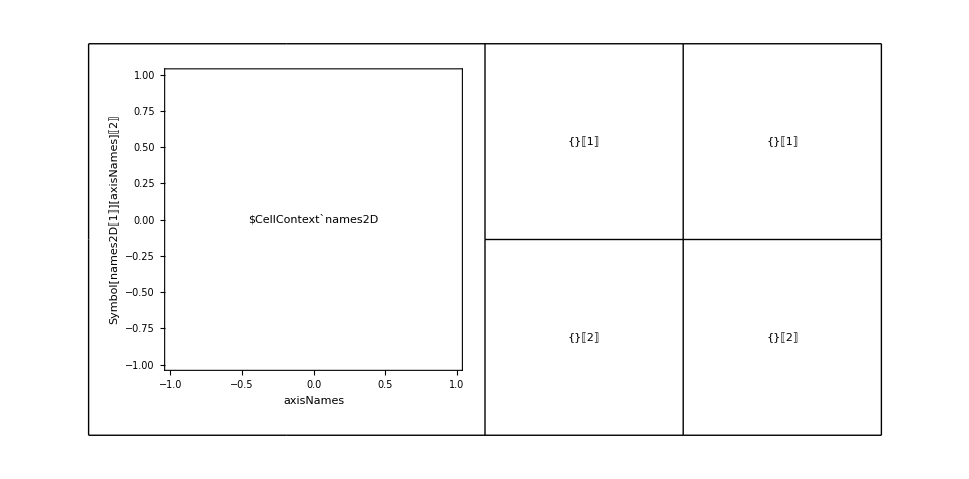

```mathematica
Block[{margin=2,dr,windows,blobPlt,blobsPlt,blobsDespecPlt},
dr=Table[ 
 Transpose[dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}}],
{i,3,Length[names2D]}];
windows=Flatten[{EdgeForm[Black],FaceForm[],Table[ 
 {Rectangle[Sequence@@(dr[[i]])],Text[ToString[i],{dr[[i,1,1]],dr[[i,2,2]]},{-1,-1}]},
{i,1,Length[dr]}]}];

blobPlt = Graphics[{windows,
Symbol[names2D[[1]]]["PlotData"]},Frame->True,PlotRange-> Symbol[names2D[[1]]]["PlotRange"],
FrameLabel->{{(Symbol[names2D[[1]]]["axisNames"])[[2]],""},{(Symbol[names2D[[1]]]["axisNames"])[[1]],Symbol[names2D[[1]]]["PlotLabel"]}}];

blobsPlt = Table[
Graphics[{
Symbol[names2D[[1]]]["PlotData"]},Frame->True,PlotRange-> Transpose[dr[[i-2]]],
FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]], ToString[i-2]}}],
{i,3,Length[names2D]}];

blobsDespecPlt = Table[
Graphics[{
Symbol[names2D[[i]]]["PlotData"]},Frame->True,PlotRange-> Transpose[dr[[i-2]]],
FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]], ToString[i-2]<>" Despeckled"}}],
{i,3,Length[names2D]}];

GraphicsGrid[{{blobPlt,SpanFromLeft,blobsPlt[[1]],blobsDespecPlt[[1]]},{SpanFromAbove,SpanFromBoth,blobsPlt[[2]],blobsDespecPlt[[2]]}},Frame->All]
]
```

### Surface plots

```mathematica
Block[{dr,hist,histoPlt,surfHistPlt},
dr=Round[dataRange[Symbol[names2D[[2]]],"All"]];
hist=HistoPlot3D[Symbol[names2D[[2]]],"LCaCb",N[1/1024],dr];
histoPlt=Graphics3D[hist,Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];
surfHistPlt=ListPlot3D[Transpose[Symbol[names2D[[2]]]["fBin"]],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,x,y}]],AxesLabel->{"Ca","Cb","f"},PlotRange->dr];
GraphicsRow[{histoPlt,surfHistPlt}]
]
```

ArcTan::indet: Indeterminate expression ArcTan[0., 0.] encountered.

-Graphics-

## 7. Find the Blobs

```mathematica
stage=7;
matLabNames=matLabNames2D[[stage-4;;]]
names=names2D[[stage-4;;]]
```

{RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2,RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1}

{RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob2,RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob1}

### Load previously generated data

#### Clear previously generated data

```mathematica
Clear[Evaluate[name],Evaluate[name<>"Frames"]]
```

#### Load previously generated data

```mathematica
Do[Print["Getting : "<> names2D[[i]]<>" -> "<>path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"];
Get[path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m"],
{i,3,Length[names2D]}];
```

Getting : RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob2 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/Hands/Orig/mathematica/Data/RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob2.m

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

Getting : RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob1 -> /Users/jaspershemilt/Developer/projects/Color-Space-Stats/matLab/ColorSpaceStats/Skin/IndividualSkin/FSkin/Hands/Orig/mathematica/Data/RGB_FSkin_Hand_Bin_Skinned_Rot_TopTail_CaCb_Despec_blob1.m

Partition::ilsmp: Single or list of positive machine-sized integers expected at position 2 of Partition[{}, 0.].

General::stop: Further output of Partition :: ilsmp will be suppressed during this calculation.

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["7. Find the Blobs","Section"]]
Do[
NotebookWrite[nb,Cell[BoxData[RowBox[{"Get","[",ToBoxes[(path<>"Data"<>"/"<>matLabNames2D[[i]]<>".m")],"]",";"}]],"Input"] ],
{i,3,Length[names2D]}];
```

```mathematica
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"margin","=","2"}],",","blobPlt",",","blobsPlt"}],"}"}],",",RowBox[{RowBox[{"blobPlt","=",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"EdgeForm","[","Black","]"}],",",RowBox[{"FaceForm","[","]"}],",",RowBox[{"Table","[",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{"Transpose","[",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}],"]"}]}],";",RowBox[{"{",RowBox[{RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","2",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}],",",RowBox[{"Rectangle","[",RowBox[{"Sequence","@@",RowBox[{"(","dr",")"}]}],"]"}],",",RowBox[{"Text","[",RowBox[{RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","1"}],",",RowBox[{"-","1"}]}],"}"}]}],"]"}]}],"}"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],"}"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotData\>\"","]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[2]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[2]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{names2D[[2]],"[","\"\<PlotLabel\>\"","]"}]}],"}"}]}],"}"}]}]}],"]"}]}],";","
",RowBox[{"blobsPlt","=",RowBox[{"Table","[","
",RowBox[{RowBox[{RowBox[{"dr","=",RowBox[{RowBox[{"dataRange","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","\"\<All\>\""}],"]"}],"+",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"-","margin"}],",","margin"}],"}"}]}],"}"}]}]}],";","
",RowBox[{"Graphics","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"elipsePlt","[",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],",","2",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],"}"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ","dr"}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"StringTake","[",RowBox[{RowBox[{RowBox[{"Symbol","[",RowBox[{"names2D","[",RowBox[{"[","i","]"}],"]"}],"]"}],"[","\"\<PlotLabel\>\"","]"}],",",RowBox[{"-","5"}]}],"]"}]}],"}"}]}],"}"}]}]}],"]"}]}],",","
",RowBox[{"{",RowBox[{"i",",","3",",",RowBox[{"Length","[","names2D","]"}]}],"}"}]}],"]"}]}],";","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{"blobPlt",",","SpanFromLeft",",",RowBox[{"blobsPlt","[",RowBox[{"[","1","]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",",RowBox[{"blobsPlt","[",RowBox[{"[","2","]"}],"]"}]}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}]}],"
","]"}]],"Input"]
]
```

### Plot the Bin

```mathematica
Block[{margin=2,blobPlt,blobsPlt},blobPlt=Graphics[{Flatten[{EdgeForm[Black],FaceForm[],Table[dr=Transpose[dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}}];{elipsePlt[Symbol[names2D[[i]]],2,{2,1}],Rectangle[Sequence@@(dr)],Text[StringTake[Symbol[names2D[[i]]]["PlotLabel"],-5],{dr[[1,1]],dr[[2,2]]},{-1,-1}]},
{i,3,Length[names2D]}]}],Symbol[names2D[[stage-5]]]["PlotData"]},Frame->True,PlotRange-> Symbol[names2D[[stage-5]]]["PlotRange"],FrameLabel->{{(Symbol[names2D[[stage-5]]]["axisNames"])[[2]],""},{(Symbol[names2D[[stage-5]]]["axisNames"])[[1]],Symbol[names2D[[stage-5]]]["PlotLabel"]}}];
blobsPlt=Table[
dr=dataRange[Symbol[names2D[[i]]],"All"]+{{-margin,margin},{-margin,margin}};
Graphics[{Symbol[names2D[[i]]]["PlotData"],elipsePlt[Symbol[names2D[[i]]],2,{2,1}]},Frame->True,PlotRange-> dr,FrameLabel->{{(Symbol[names2D[[i]]]["axisNames"])[[2]],""},{(Symbol[names2D[[i]]]["axisNames"])[[1]],StringTake[Symbol[names2D[[i]]]["PlotLabel"],-5]}}],
{i,3,Length[names2D]}];
GraphicsGrid[{{blobPlt,SpanFromLeft,blobsPlt[[1]]},{SpanFromAbove,SpanFromBoth,blobsPlt[[2]]}},Frame->All]
]
```

-Graphics-

```mathematica
GraphicsGrid[Table[{denPlt[i],Graphics[Symbol[names[[i]]]["PlotData"],Frame->True,PlotRange-> Symbol[names[[i]]]["PlotRange"],FrameLabel->{{(Symbol[names[[i]]]["axisNames"])[[2]],""},{(Symbol[names[[i]]]["axisNames"])[[1]],Symbol[names[[i]]]["PlotLabel"]}}]},
{i,1,Length[names]}]]
```

## 8. Fit the Gaussian

```mathematica
blob=0;
name=names2D[[3+blob]]
```

RGBFSkinHandBinSkinnedRotTopTailCaCbDespecblob2

### Generate the Plot Notebook

```mathematica
NotebookWrite[nb,Cell["8. Fit the Gaussian","Section"]]
```

```mathematica
Do[
NotebookWrite[nb,Cell["Blob : "<>ToString[blob],"Subsection"]];
NotebookWrite[nb,Cell[BoxData[RowBox[{"Block","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"blob","=","0"}],",","redPlt",",","greenPlt",",","denPlt",",","denOpacityPlt",",","axesPlt",",","elpsPlt",",","thetaPlt",",","thetaPi2Plt",",","histoPlt",",","fitPlt",",","combPlt3D",",","aspctRatio",",","combPlt",",","overviewPlt"}],"}"}],",","
",RowBox[{RowBox[{"redPlt","=",RowBox[{"fitXPlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],";","
",RowBox[{"greenPlt","=",RowBox[{"fitYPlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],";","
","
",RowBox[{"denPlt","=",RowBox[{"ListDensityPlot","[",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<fBin\>\"","]"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Cb\>\"",",","\"\<Ca\>\""}],"}"}]}],",",RowBox[{"InterpolationOrder","→","0"}]}],"]"}]}],";","
",RowBox[{"denOpacityPlt","=",RowBox[{"Graphics","[",RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<PlotData\>\"","]"}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"PlotRange","→"," ",RowBox[{names2D[[3+blob]],"[","\"\<PlotRange\>\"","]"}]}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","2","]"}],"]"}],",","\"\<\>\""}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{RowBox[{"(",RowBox[{names2D[[3+blob]],"[","\"\<axisNames\>\"","]"}],")"}],"[",RowBox[{"[","1","]"}],"]"}],",","\"\<Overview\>\""}],"}"}]}],"}"}]}]}],"]"}]}],";","
","
",RowBox[{"axesPlt","=",RowBox[{"Graphics","[",RowBox[{"fit2DLinesPlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],"]"}],"]"}]}],";","
","
",RowBox[{"elpsPlt","=",RowBox[{"Graphics","[",RowBox[{"elipsePlt","[",RowBox[{names2D[[3+blob]],",","5",",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}],"]"}]}],";","
","
",RowBox[{RowBox[{"{",RowBox[{"thetaPlt",",","thetaPi2Plt"}],"}"}],"=",RowBox[{"fit2DAnglePlt","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"2",",","1"}],"}"}]}],"]"}]}],";","
","
",RowBox[{"dr","=",RowBox[{"Round","[",RowBox[{"dataRange","[",RowBox[{names2D[[3+blob]],",","\"\<All\>\""}],"]"}],"]"}]}],";","
",RowBox[{"histoPlt","=",RowBox[{"Graphics3D","[",RowBox[{RowBox[{"HistoPlot3D","[",RowBox[{names2D[[3+blob]],",","\"\<LCaCb\>\"",",",RowBox[{"N","[",RowBox[{"1","/","1024"}],"]"}],",","dr"}],"]"}],",",RowBox[{"Lighting","→","\"\<Neutral\>\""}],",",RowBox[{"Axes","->","True"}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"BoxRatios","→",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"Max","[",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],"]"}]}],"]"}],",","1"}],"}"}],"]"}]}]}],"]"}]}],";","
",RowBox[{"fun","=",RowBox[{"GaussianFit","[",RowBox[{names2D[[3+blob]],",",RowBox[{"{",RowBox[{"1",",","2"}],"}"}]}],"]"}]}],";","
",RowBox[{"fitPlt","=",RowBox[{"Plot3D","[",RowBox[{RowBox[{"fun","[",RowBox[{"x",",","y"}],"]"}],",",RowBox[{"{",RowBox[{"x",",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{"y",",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}],",",RowBox[{"PlotRange","→",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"}"}]}],",",RowBox[{"PlotPoints","→",RowBox[{"2"," ",RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}]}],")"}]}]}],",",RowBox[{"PlotStyle","→",RowBox[{"LCaCbColor","[",RowBox[{"{",RowBox[{"0.7",",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<gMean\>\"","]"}],"[",RowBox[{"[","1","]"}],"]"}],"/","255"}],",",RowBox[{RowBox[{RowBox[{names2D[[3+blob]],"[","\"\<gMean\>\"","]"}],"[",RowBox[{"[","2","]"}],"]"}],"/","255"}],",","0.6"}],"}"}],"]"}]}],",",RowBox[{"AxesLabel","→",RowBox[{"{",RowBox[{"\"\<Ca\>\"",",","\"\<Cb\>\"",",","\"\<f\>\""}],"}"}]}],",",RowBox[{"MeshFunctions","->",RowBox[{"{",RowBox[{"#3","&"}],"}"}]}]}],"]"}]}],";","
",RowBox[{"combPlt3D","=",RowBox[{"Show","[",RowBox[{RowBox[{"{",RowBox[{"fitPlt",",","histoPlt"}],"}"}],",","
",RowBox[{"PlotRange","→",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[","1","]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[","2","]"}],"]"}],",",RowBox[{"{",RowBox[{"0",",","1"}],"}"}]}],"}"}]}],",","
",RowBox[{"BoxRatios","→",RowBox[{"Flatten","[",RowBox[{"{",RowBox[{RowBox[{"N","[",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"Max","[",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"All",",","1"}],"]"}],"]"}]}],"]"}]}],"]"}],",","1"}],"}"}],"]"}]}]}],"]"}]}],";","
","
",RowBox[{"dr","=",RowBox[{"dataRange","[",RowBox[{names2D[[3+blob]],",","5"}],"]"}]}],";","
",RowBox[{"aspctRatio","=",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}]}],")"}]}]}],";","
",RowBox[{"combPlt","=",RowBox[{"Show","[",RowBox[{RowBox[{"{",RowBox[{"denOpacityPlt",",","axesPlt",",","elpsPlt",",","
","thetaPlt"}],"}"}],",",RowBox[{"PlotRange","→","dr"}],",",RowBox[{"AspectRatio","→",RowBox[{RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}]}],")"}],"/",RowBox[{"(",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],"-",RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}]}],")"}]}]}],",",RowBox[{"Frame","→","True"}],",",RowBox[{"FrameLabel","→",RowBox[{"{",RowBox[{"\"\<Cb\>\"",",","\"\<Ca\>\""}],"}"}]}]}],"]"}]}],";","
",RowBox[{"overviewPlt","=",RowBox[{"Show","[",RowBox[{"{",RowBox[{"denOpacityPlt",",",RowBox[{"Graphics","[",RowBox[{"{",RowBox[{RowBox[{"FaceForm","[","]"}],",",RowBox[{"EdgeForm","[",RowBox[{"{",RowBox[{"Black",",",RowBox[{"Opacity","[","1","]"}]}],"}"}],"]"}],",",RowBox[{"Rectangle","[",RowBox[{RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","1"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","1"}],"]"}],"]"}]}],"}"}],",",RowBox[{"{",RowBox[{RowBox[{"dr","[",RowBox[{"[",RowBox[{"1",",","2"}],"]"}],"]"}],",",RowBox[{"dr","[",RowBox[{"[",RowBox[{"2",",","2"}],"]"}],"]"}]}],"}"}]}],"]"}]}],"}"}],"]"}]}],"}"}],"]"}]}],";","
","
",RowBox[{"TabView","[",RowBox[{"{",RowBox[{RowBox[{"If","[",RowBox[{RowBox[{"aspctRatio","≥","1"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D",",","         ","SpanFromLeft",",","combPlt",",","             ","SpanFromLeft",",","overviewPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","redPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt3D",",","SpanFromLeft",",","combPlt",",","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromAbove",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromLeft",",","overviewPlt",",","redPlt",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}],"]"}],",","
",RowBox[{"If","[",RowBox[{RowBox[{"aspctRatio","≥","1"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt",",","             ","SpanFromLeft",",","overviewPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","redPlt"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}],",","
",RowBox[{"GraphicsGrid","[",RowBox[{RowBox[{"{","
",RowBox[{RowBox[{"{",RowBox[{"combPlt",",","SpanFromLeft",",","SpanFromLeft"}],"}"}],",","
",RowBox[{"{",RowBox[{"SpanFromAbove",",","SpanFromBoth",",","SpanFromBoth"}],"}"}],",","
",RowBox[{"{",RowBox[{"overviewPlt",",","redPlt",",","greenPlt"}],"}"}]}],"}"}],",",RowBox[{"Frame","→","All"}]}],"]"}]}],"]"}]}],"}"}],"]"}]}]}],"
","]"}]],"Input"]
],{blob,0,Length[names2D]-3}]
```

### Check the Data

Set the important data to simple variable names.

```mathematica
μ={Symbol[name]["gMean"][[1]],Symbol[name]["gMean"][[2]]}
σ={Symbol[name]["gSigma"][[1]],Symbol[name]["gSigma"][[2]]}
θ=Symbol[name]["gTheta"]
```

Check that the axes max values are close to the mean

```mathematica
{CaMax,CbMax}=Position[Symbol[name]["fBin"],n_/;n==1.][[1]];
Row[{CaMax ,"==",μ[[1]]}]
Row[{CbMax,"==",μ[[2]]}]
```

### Density Plot

```mathematica
SetUpLCaCbColor[0];
```

```mathematica
x=Graphics[Circle[]];
GraphicsGrid[{{x,SpanFromLeft,x},{SpanFromAbove,SpanFromBoth,x},{SpanFromAbove,SpanFromBoth,x}},Frame->All]
GraphicsGrid[{{x,SpanFromLeft,SpanFromLeft},{SpanFromAbove,SpanFromBoth,SpanFromBoth},{x,x,x}},Frame->All]
GraphicsGrid[{
{x,                           SpanFromLeft,x                         , SpanFromLeft,x},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,x},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,x}},Frame->All]
```

```mathematica
Block[{blob=0,redPlt,greenPlt,denPlt,denOpacityPlt,axesPlt,elpsPlt,thetaPlt,thetaPi2Plt,histoPlt,fitPlt,combPlt3D,aspctRatio,combPlt,overviewPlt},
redPlt=fitXPlt[Symbol[names2D[[3+blob]]],5,{2,1}];
greenPlt=fitYPlt[Symbol[names2D[[3+blob]]],5,{2,1}];

denPlt=ListDensityPlot[Symbol[names2D[[3+blob]]]["fBin"],AxesLabel->{"Cb","Ca"},InterpolationOrder->0];
denOpacityPlt=Graphics[Symbol[names2D[[3+blob]]]["PlotData"],Frame->True,PlotRange-> Symbol[names2D[[3+blob]]]["PlotRange"],FrameLabel->{{(Symbol[names2D[[3+blob]]]["axisNames"])[[2]],""},{(Symbol[names2D[[3+blob]]]["axisNames"])[[1]],"Overview"}}];

axesPlt=Graphics[fit2DLinesPlt[Symbol[names2D[[3+blob]]],5,{1,2}]];

elpsPlt=Graphics[elipsePlt[Symbol[names2D[[3+blob]]],5,{2,1}]];

{thetaPlt,thetaPi2Plt}=fit2DAnglePlt[Symbol[names2D[[3+blob]]],{2,1}];

dr=Round[dataRange[Symbol[names2D[[3+blob]]],"All"]];
histoPlt=Graphics3D[HistoPlot3D[Symbol[names2D[[3+blob]]],"LCaCb",N[1/1024],dr],Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];
fun=GaussianFit[Symbol[names2D[[3+blob]]],{1,2}];
fitPlt=Plot3D[fun[x,y],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange->{dr[[1]],dr[[2]],{0,1}},PlotPoints->2 (dr[[1,2]]-dr[[1,1]]),PlotStyle->LCaCbColor[{0.7,Symbol[names2D[[3+blob]]]["gMean"][[1]]/255,Symbol[names2D[[3+blob]]]["gMean"][[2]]/255,0.6}],AxesLabel->{"Ca","Cb","f"},MeshFunctions->{#3&}];
combPlt3D=Show[{fitPlt,histoPlt},
PlotRange->{dr[[1]],dr[[2]],{0,1}},
BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];

dr=dataRange[Symbol[names2D[[3+blob]]],5];
aspctRatio=(dr[[2,2]]-dr[[2,1]])/(dr[[1,2]]-dr[[1,1]]);
combPlt=Show[{denOpacityPlt,axesPlt,elpsPlt,
thetaPlt},PlotRange->dr,AspectRatio->(dr[[2,2]]-dr[[2,1]])/(dr[[1,2]]-dr[[1,1]]),Frame->True,FrameLabel->{"Cb","Ca"}];
overviewPlt=Show[{denOpacityPlt,Graphics[{FaceForm[],EdgeForm[{Black,Opacity[1]}],Rectangle[{dr[[1,1]],dr[[2,1]]},{dr[[1,2]],dr[[2,2]]}]}]}];

TabView[{If[aspctRatio≥1,
GraphicsGrid[{
{combPlt3D,         SpanFromLeft,combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All],
GraphicsGrid[{
{combPlt3D,SpanFromLeft,combPlt,SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromAbove,SpanFromBoth},
{SpanFromLeft,overviewPlt,redPlt,greenPlt}},Frame->All]],
If[aspctRatio≥1,
GraphicsGrid[{
{combPlt,             SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All],
GraphicsGrid[{
{combPlt,SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromBoth},
{overviewPlt,redPlt,greenPlt}},Frame->All]]}]
]
```

12

```mathematica
Clear[mmAxis]
Block[{redPlt,greenPlt},
redPlt=fitXPlt[Symbol[name],5,{1,2}];
greenPlt=fitYPlt[Symbol[name],5,{1,2}];

denPlt=ListDensityPlot[Symbol[name]["fBin"],AxesLabel->{"Cb","Ca"},InterpolationOrder->0];
denOpacityPlt=Graphics[Symbol[name]["PlotData"],Frame->True,PlotRange-> Symbol[name]["PlotRange"],FrameLabel->{{(Symbol[name]["axisNames"])[[2]],""},{(Symbol[name]["axisNames"])[[1]],Symbol[name]["PlotLabel"]}}];

axesPlt=Graphics[fit2DLinesPlt[Symbol[name],5,{2,1}]];

elpsPlt=Graphics[elipsePlt[Symbol[name],5]];

{thetaPlt,thetaPi2Plt}=fit2DAnglePlt[Symbol[name],{1,2}];

dr=Reverse[dataRange[Symbol[name],5]];
aspctRatio=(dr[[2,2]]-dr[[2,1]])/(dr[[1,2]]-dr[[1,1]]);
combPlt=Show[{denPlt,axesPlt,elpsPlt,
thetaPlt},PlotRange->dr,AspectRatio->aspctRatio,Frame->True,FrameLabel->{"Cb","Ca"}];
overviewPlt=Show[{denPlt,Graphics[{FaceForm[],EdgeForm[{Black,Opacity[1]}],Rectangle[{dr[[1,1]],dr[[2,1]]},{dr[[1,2]],dr[[2,2]]}]}]}];
If[aspctRatio≥1,
GraphicsGrid[{
{combPlt,SpanFromLeft,overviewPlt},
{SpanFromAbove,SpanFromBoth,redPlt},
{SpanFromAbove,SpanFromBoth,greenPlt}},Frame->All],
GraphicsGrid[{
{combPlt,SpanFromLeft,SpanFromLeft},
{SpanFromAbove,SpanFromBoth,SpanFromBoth},
{overviewPlt,redPlt,greenPlt}},Frame->All]]


]
```

Proof that the eliptical plot is the same as the contor plot

```mathematica
μ={Symbol[name]["gMean"][[1]],Symbol[name]["gMean"][[2]]}
σ={Symbol[name]["gSigma"][[1]],Symbol[name]["gSigma"][[2]]}
θ=Symbol[name]["gTheta"]

sigTicks=Table[mmPts=MajorMinorAxesPoints[Reverse[μ],σ,Pi/2-θ,i];
GaussianFit[mmPts[[1,1,1]],mmPts[[1,1,2]],Reverse[μ],σ,Pi/2+θ],{i,1,5}];
contPlt=ContourPlot[GaussianFit[x,y,Reverse[μ],σ,Pi/2+θ],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange->{dr[[1]],dr[[2]],{0,1}},Contours->sigTicks];

GraphicsRow[{Show[{contPlt,elipsePlt,axesPltPnts},Frame->True,FrameLabel->{"Cb","Ca"}],Show[{denPlt},Frame->True,FrameLabel->{"Cb","Ca"}]}]
```

### Surface plots

```mathematica
GaussianFit[Symbol[name],{1,2}]
```

```mathematica
dr=Round[dataRange[Symbol[name],"All"]];
hist=HistoPlot3D[Symbol[name],"LCaCb",N[1/1024],dr];
histoPlt=Graphics3D[hist,Lighting->"Neutral",Axes->True,AxesLabel->{"Ca","Cb","f"},BoxRatios->Flatten[{N[(dr[[All,2]]-dr[[All,1]])/Max[dr[[All,2]]-dr[[All,1]]]],1}]];
surfHistPlt=ListPlot3D[Transpose[Symbol[name]["fBin"]],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,x,y}]],AxesLabel->{"Ca","Cb","f"},PlotRange->dr];
fun=GaussianFit[Symbol[name],{1,2}];
fitPlt=Plot3D[fun[x,y],{x,dr[[1,1]],dr[[1,2]]},{y,dr[[2,1]],dr[[2,2]]},PlotRange->{dr[[1]],dr[[2]],{0,1}},PlotPoints->2 (dr[[1,2]]-dr[[1,1]]),PlotStyle->LCaCbColor[{0.7,μ[[1]]/255,μ[[2]]/255,0.6}],AxesLabel->{"Ca","Cb","f"}];
GraphicsRow[{Show[{histoPlt,fitPlt}],Show[{surfHistPlt,fitPlt}]}]
```

### Surface plots

```mathematica
ListPlot3D[Symbol[name]["fBin"],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,y,x}]],AxesLabel->{"Cb","Ca","f"}]
```

```mathematica
ListPlot3D[Symbol[name]["fBin"],ColorFunction->Function[{x,y,z},LCaCbColor[{0.5,y,x}]],PlotRange->{{μ[[2]]-10 σ[[1]],μ[[2]]+10 σ[[1]]},{μ[[1]]-10 σ[[2]],μ[[1]]+10 σ[[2]]},{0,1}},AxesLabel->{"Cb","Ca","f"}]
```

## That RGB Image check thing.

```mathematica
img=-Graphics-;
```

```mathematica
imgData=Flatten[ImageData[img,"Byte"],1];
```

```mathematica
bins=ConstantArray[0,{256,256,256}];
```

```mathematica
Do[
bins[[ imgData[[i,1]]+1, imgData[[i,2]]+1, imgData[[i,3]]+1 ]]++;
,{i,1,Dimensions[imgData][[1]] }]
```

```mathematica
Dimensions[bins]
```

```mathematica
Max[Flatten[bins]]
```

```mathematica
Position[bins,n_/;n==5]
```

```mathematica
pos=Position[ImageData[img,"Byte"],n_/;n=={0,255,255}]
```

Are they all really {0,255,255}

```mathematica
Table[ImageData[img,"Byte"][[pos[[i,1]],pos[[i,2]]]],{i,1,Length[pos]}]
```

```mathematica
Count[bins,n_/;n>1,3]
```

```mathematica
Dimensions[ImageData[img,"Byte"]]
```

```mathematica
Show[{img,Graphics[{Table[Circle[pos[[i]],10],{i,1,Length[pos]}]}]}]
```